```mathematica
Solve[x^2+9*x+2==0,x]
```

{{x→1/2 (-9-√73)},{x→1/2 (-9+√73)}}

```mathematica
Solve[x^2+9*x+2==0,x]
```

{{x→1/2 (-9-√73)},{x→1/2 (-9+√73)}}

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
NSolve[a*x^3+b*x^2+c*x+d==0,x]
```

{{x→-(0.333333 b)/a+((0.209987-0.363708 ⅈ) (-1. b^2+3. a c))/(a (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3))-1/a(0.132283+0.229122 ⅈ) (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3)},{x→-(0.333333 b)/a+((0.209987+0.363708 ⅈ) (-1. b^2+3. a c))/(a (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3))-1/a(0.132283-0.229122 ⅈ) (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3)},{x→-(0.333333 b)/a-(0.419974 (-1. b^2+3. a c))/(a (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3))+1/a 0.264567 (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3)}}

```mathematica
NSolve[x^5+16*x^4+7*x^3+17*x^2+11*x+5==0,x]
```

{{x→-15.6187},{x→-0.386706-0.39778 ⅈ},{x→-0.386706+0.39778 ⅈ},{x→0.196058-1.00086 ⅈ},{x→0.196058+1.00086 ⅈ}}

```mathematica
Solve[Sin[ArcCos[x^2-x]]==1,x]
```

{{x→0},{x→1}}

```mathematica
Solve[{5 x^2+6 y^2==9,x+y==1},{x,y}]
```

{{x→1/11 (6-√69),y→1/11 (5+√69)},{x→1/11 (6+√69),y→1/11 (5-√69)}}

```mathematica
Solve[{x+y+z==9,x+4*y==4,2*x+3*y+z==9},{x,y,z}]
```

{{x→-4,y→2,z→11}}

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

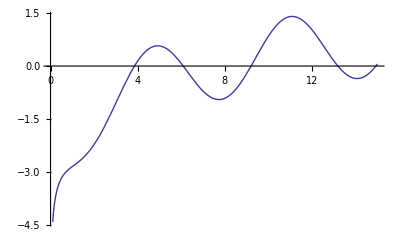

```mathematica
Plot[{Log[x]-Sin[x]-2==0},{x,0,15}]
```

```mathematica
FindRoot[{Log[x]-Sin[x]-2==0},{x,4}]
```

{x→3.85128}

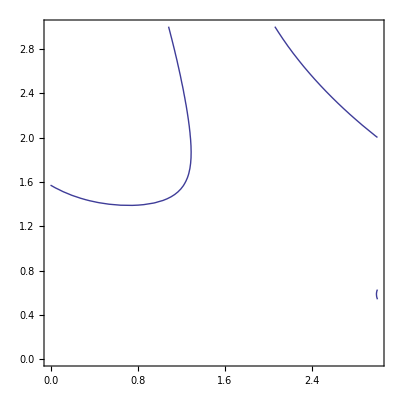

```mathematica
a=ContourPlot[{Sin[x*y]==Sin[x]+Cos[y]},{x,0,3},{y,0,3}]
```

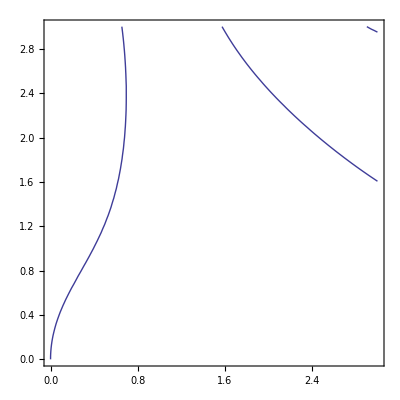

```mathematica
b=ContourPlot[{Cos[x*y]==Sin[x]+Cos[y]},{x,0,3},{y,0,3}]
```

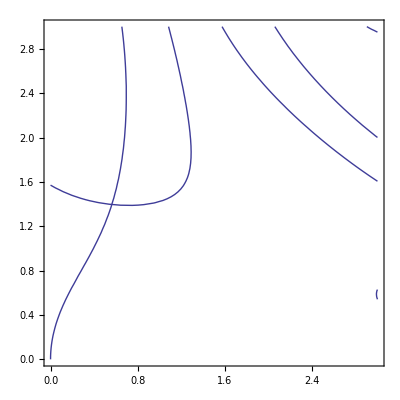

```mathematica
Show[a,b]
```

```mathematica
FindRoot[{{Sin[x*y]==Sin[x]+Cos[y]},{Cos[x*y]==Sin[x]+Cos[y]}},{x,0.6},{y,1.4}]
```

{x→0.562547,y→1.39615}